## 1/29/19 v3 lab section

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/dannytoomey/Documents/Classes/Winter 2019/Psy 113L/my workbooks

```mathematica
img=Import["testImage2.tif"]
```

-Graphics-

```mathematica
(*midterm review*)



(*question 1 - calculate sin of the log of 10 with base e and produce a calculator like output*)


Sin[Log[10]]//N     (*don't need to specify base  e b/c base e is default in mathematica*)
```

0.74398

```mathematica
Sin[Log[10,10]]//N
```

0.841471

```mathematica
Log[10,10]//N
```

1.

```mathematica
Log[10.]
```

2.30259

```mathematica
Log[10]//N
```

2.30259

```mathematica
N[Log[10]]
```

2.30259

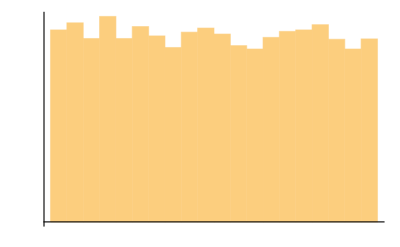

```mathematica
(*question 2 - produce 10,000 random numbers in the range of 0,1 and plot histogram w/o showing numbers on screen*)


Histogram[RandomReal[{0,1},10000],Ticks->None]
```

```mathematica
(*question 3 - produce a list of 5 text items and retrive the third item*)


a={"one","two","three","four","five"};
a[[3]]
```

three

```mathematica
a={{"one","two","apple"},{"four","five","six"}};
a[[2,2]]
```

five

```mathematica
Position[{a},"apple"]
```

{{1,1,3}}

```mathematica
(* question 4 - the following command tried to use a built-in function 
	bernoulliB(2)
find the errors to make it work*)
```

```mathematica
BernoulliB[2]
```

1/6

```mathematica
(*question 5 - What is the output of the following commands?
A=2;
	B=3;
	A=B;
	B=A;
	B *)



3
```

```mathematica
A=2;
	B=3;
	A=B;
	B=A;
	B
```

3

```mathematica
(*question 5 - What is the output of the following commands?
A=2;
	B=3;
	A=B;
	B=A;
	A==B *)
1 (*true*)
```

```mathematica
A=2;
	B=3;
	A=B;
	B=A;
	A==B
```

True

```mathematica
(*question 7 - create an array of the square of numbers ranging from 10 to 20*)




Table[n^2,{n,10,20}]
```

{100,121,144,169,196,225,256,289,324,361,400}

```mathematica
(*question 8 - the following attempts to add two arrays, element-wise, but produces a strange output:
(7;8;9;10)+(4;2;9;0)
fix it*)

a={7,8,9,10};
b={4,2,9,0};
a+b
```

{11,10,18,10}

```mathematica
a={1,2,3,4};
Transpose[{a}]
```

{{1},{2},{3},{4}}

```mathematica
Column[{a}]
```

{1,2,3,4}

```mathematica
a={1,2,3,4};
Column[a]
```

1
2
3
4

```mathematica
(*write down the predicted output of the following command
For[i=1,i≤4,Print[i,"is here!"],i++] *)
```

```mathematica
"is here!"
"is here!"
"is here!"
"is here!"
```

```mathematica
For[i=0,i<4,Print[i,"is here!"],i++]
```

1is here!

2is here!

3is here!

4is here!

```mathematica
For[i=0,i<4,i++,Print[i,"is here!"]]
```

0is here!

1is here!

2is here!

3is here!

```mathematica
(* why doesn't this work???*)



For[i=0,I<4, Print[i,"is here!"],i++]
```